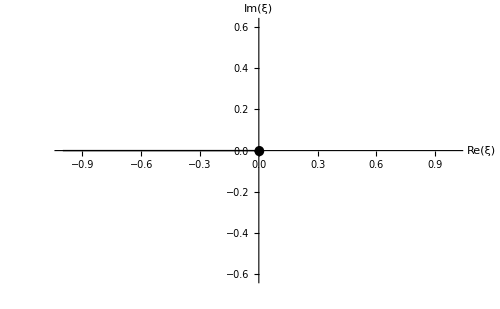

```mathematica
p1=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[ξ],Im[ξ]},Epilog->{{Thick,Line[{{-1,0},{0,0}}]},Disk[{0,0},0.025]},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->14,Black},ImageSize->500]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_lower_singularities.eps",p1];
```

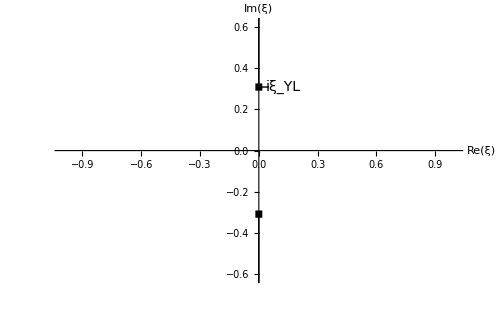

```mathematica
p2=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[ξ],Im[ξ]},Epilog->{{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],
Line[{{0,1/GoldenRatio/2},{0.05,1/GoldenRatio/2}}],
{Black,Text[Style["iξ_YL",FontSize->14,Black,FontFamily->"Times"], {0.125,1/GoldenRatio/2}]}
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->14,Black},ImageSize->500]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_higher_singularities.eps",p2];
```

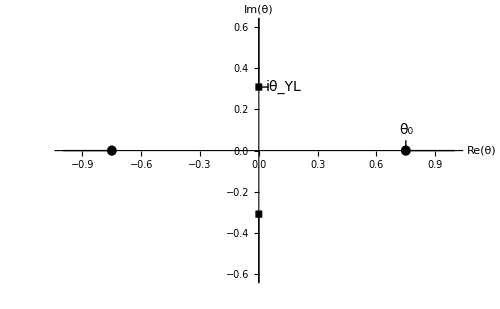

```mathematica
p3=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[θ],Im[θ]},Epilog->{{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],{Thick,Line[{{-1,0},{-0.75,0}}]},Disk[{-0.75,0},0.025],{Thick,Line[{{1,0},{0.75,0}}]},Disk[{0.75,0},0.025],
Line[{{0.75,0},{0.75,0.05}}],
Line[{{0,1/GoldenRatio/2},{0.05,1/GoldenRatio/2}}],
{Black,Text[Style["iθ_YL",FontSize->14,Black,FontFamily->"Times"], {0.125,1/GoldenRatio/2}]},
{Black,Text[Style["θ_0",FontSize->14,Black,FontFamily->"Times"], {0.75,0.1}]}
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->14,Black},ImageSize->500]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_theta_singularities.eps",p3];
```

```mathematica
p4=Plot[√(0.95^2-x^2)/GoldenRatio,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Red},AxesLabel->{Re[θ'],Im[θ']},Prolog->{
{Thickness[0.004],Red,Line[{{-0.95,0.0075},{-0.8,0.0075}}]},
{Thickness[0.004],Red,Circle[{-0.75,0},0.05,{0,π}]},
{Thickness[0.004],Red,Line[{{0.8,0.0075},{0.95,0.0075}}]},
{Thickness[0.004],Red,Circle[{0.75,0},0.05,{0,π}]},
{Thickness[0.004],Red,Line[{{-0.7,0},{0.-0.05,0}}]},
{Thickness[0.004],Red,Circle[{0,0},0.05,{0,π}]},
{Thickness[0.004],Red,Line[{{0.05,0},{0.25,0}}]},
{Thickness[0.004],Red,Circle[{0.3,0},0.05,{0,π}]},
{Thickness[0.004],Red,Line[{{0.35,0},{0.7,0}}]},
{Thickness[0.004],Red,Line[{{0.0075,1/GoldenRatio 0.95},{0.0075,1/GoldenRatio/2+0.05}}]},
{Thickness[0.004],Red,Line[{{-0.0075,1/GoldenRatio 0.95},{-0.0075,1/GoldenRatio/2+0.05}}]},
{Thickness[0.004],Red,Circle[{0,1/GoldenRatio/2},0.05]},
Line[{{0.3,0},{0.3,-0.05}}],
{Black,Text[Style["θ",FontSize->14,Black,FontFamily->"Times"], {0.3,-0.1}]}},
Epilog->{
{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],
Rotate[RegularPolygon[{0,0},0.025,4],π/4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],{Thick,Line[{{-1,0},{-0.75,0}}]},Disk[{-0.75,0},0.025],{Thick,Line[{{1,0},{0.75,0}}]},Disk[{0.75,0},0.025],
Polygon[{0.3,0}+#&/@SortBy[0.025/1.5Join[CirclePoints[5],-CirclePoints[5]/2],ArcTan@@#&]]
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->14,Black},ImageSize->500]
```

-Graphics-

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/contour_path.eps",p4];
```

```mathematica
ℐ2[θc_,B_][θ_]:=(θ-θc)Exp[-1/(B(θ-θc))]
ℛ2[θc_,B_][θ_]:=1/π(θc Exp[1/(B θc)]ExpIntegralEi[-1/(B θc)]+(θ-θc)Exp[-1/(B(θ-θc))]ExpIntegralEi[1/(B(θ-θc))])
ℱc2[θc_,B_,Fc_][θ_]:=Fc(ℛ2[θc,B][θ]+ℛ2[θc,B][-θ]+ⅈ Sign[Im[θ]](ℐ2[θc,B][θ]-ℐ2[θc,B][-θ]))
ℱc2n[θc_,B_,Fc_][θ_]:=ℱc2[θc,B,Fc][θ]/;NumericQ[θ]
```

```mathematica
ℱc3[θc_,B_,Fc_][θ_]:=Fc(θc^2-θ^2)^(-7/3)Exp[-1/(B(θc^2-θ^2))^2]
```

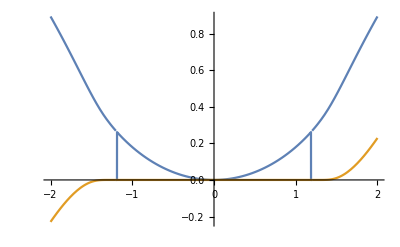

```mathematica
Plot[Evaluate[ReIm@ℱc2[1+2/10,1,1][θ+10^-10 ⅈ]],{θ,-2,2},WorkingPrecision->30,PlotPoints->100]
```

```mathematica
ComplexPlot[ℱc2n[1.2,1,1][θ],{θ,-4-4ⅈ,4+4ⅈ},ColorFunction->None,Exclusions->{{Im[θ]==0,Re[θ]^2>1.2^2}}]
```

-Graphics-

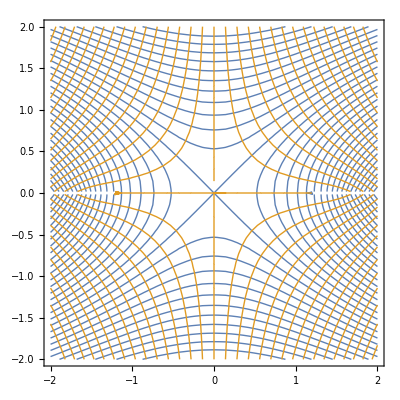

```mathematica
ComplexContourPlot[ReIm@ℱc2n[1.2,1,1][θ],{θ,-2-2ⅈ,2+2ⅈ},ColorFunction->None,Exclusions->{{Im[θ]==0,Re[θ]^2>1.2^2}},Contours->30]
```

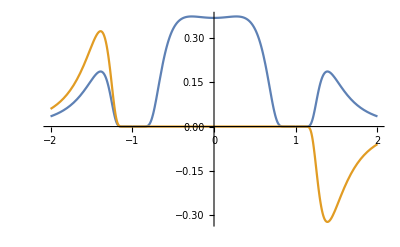

```mathematica
Plot[Evaluate[ReIm@ℱc3[1,1,1][θ-10^-10 ⅈ]],{θ,-2,2},WorkingPrecision->20,PlotPoints->100]
```

```mathematica
ComplexPlot[ℱc3[1.2,1,1][θ]-11(0.18^2+θ^2)^(1+0.085),{θ,-2-2ⅈ,2+2ⅈ},ColorFunction->None,Exclusions->{{Im[θ]==0,Re[θ]^2>1.2^2},{Re[θ]==0,Im[θ]^2>0.18^2}},PlotPoints->50]
```

-Graphics-

```mathematica
Series[(θc^2-θ^2)^(-7/3),{θ,θc,1}]
```

(θ-θc)^(7/3)/(4 2^(1/3) (-((θ-θc) θc))^(7/3) (θ-θc)^(7/3))-(7 (θ-θc)^(7/3))/(24 (2^(1/3) θc (-((θ-θc) θc))^(7/3)) (θ-θc)^(4/3))+(35 (θ-θc)^(7/3))/(144 2^(1/3) θc^2 (-((θ-θc) θc))^(7/3) (θ-θc)^(1/3))+O[θ-θc]^(4/3)